```mathematica
遭陨石迎头碰撞,x速度减小,将怎样运动?速度增大,将怎样运动?
```

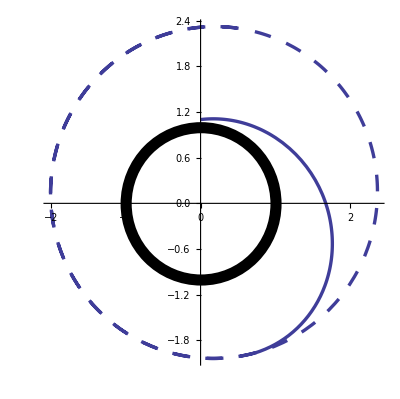

```mathematica
tm1=1;coef=4.0 π^2;
xinitial={0,6.8};yinitial={1.1,0.8};
(*.....orbit before colliding......*)
equ={x''[t]==-(coef*x[t])/((x[t]^2+y[t]^2)^(3/2)),
y''[t]==-(coef*y[t])/((x[t]^2+y[t]^2)^(3/2)),
x[0]==xinitial[[1]],x'[0]==xinitial[[2]],y[0]==yinitial[[1]],y'[0]==yinitial[[2]]};
s=NDSolve[equ,{x,y},{t,0,3*tm1}];
{x,y}={x,y}/.s[[1]];
g1=ParametricPlot[{x[t],y[t]},{t,0,tm1},
PlotStyle->Thickness[0.006],
Epilog->{Thickness[0.02],Circle[{0,0},1]}];
(*......orbit after colliding.......*)
xinitial={x[tm1],x'[tm1]*1.25};
yinitial={y[tm1],y'[tm1]*1.1};
Clear[x,y]
tm2=5;
equ={x''[t]==-(coef*x[t])/((x[t]^2+y[t]^2)^(3/2)),
y''[t]==-(coef*y[t])/((x[t]^2+y[t]^2)^(3/2)),
x[0]==xinitial[[1]],x'[0]==xinitial[[2]],y[0]==yinitial[[1]],y'[0]==yinitial[[2]]};
s=NDSolve[equ,{x,y},{t,0,tm2}];
{x,y}={x,y}/.s[[1]];
g2=ParametricPlot[{x[t],y[t]},{t,0,tm2},
PlotStyle->{Thickness[0.006],
Dashing[{0.03,0.03}]}];
Show[{g1,g2},PlotRange->All,
AxesStyle->Thickness[0.003]]
Clear[x,y,equ,s,g1,g2,coef,tm1,tm2]
```